```mathematica
ClearAll["Global`*"]
```

```mathematica
ωCs = 2 Pi*9.192631770*10^9;
Ωrf = 2 Pi*40*10^3; 
ΩuwL = 2 Pi*20*10^3;   (* The last factor is the M.E. *)
Δ=2 Pi*200*10^3; (* Detuning of two-photon transition *)
ΩuwR = ΩuwL; (* Define the amplitude ratio between different polarziations *)
Ωuwπ=ΩuwL;
ΔEhfs=9.19263770 10^9;gI=−0.000398853; gJ=2.0025403;μB=1.3996246 10^6;
E4[M_,B_]:=2Pi*ΔEhfs(-1/(2(2 7/2+1))+M/1(gI μB B)/ΔEhfs+ 1/2 √(1+(4M)/(2 7/2+1)((gJ-gI)μB B)/ΔEhfs+(((gJ-gI) μB B)/ΔEhfs)^2));
E3[M_,B_]:=2Pi*ΔEhfs(-1/(2(2 7/2+1))+M/1(gI μB B)/ΔEhfs- 1/2 √(1+(4M)/(2 7/2+1)((gJ-gI) μB B)/ΔEhfs+(((gJ-gI) μB B)/ΔEhfs)^2));
(* Define enerngy levels with Breit-Rabi formular *) 
Bq=1.39304348624747;
ωuw=E4[0,Bq]-E3[-1,Bq]+δuw; (* define the uwave frequency with detuning *)
ωrf=E4[1,Bq]-E4[0,Bq]+δrf; (* define the RF frequency with detuning *)
Ωeff =Ωrf*ΩuwL*Sqrt[15]/(16*2*Δ); (* Effective two-photon transition Rabi frequency, unit: 2π x Hz *)
TPi = 50/21*Pi/Ωeff; (* Pi pulse length, unit : s *)
TPiHalf=0.5*TPi;
Tpulse[ϕ_]:=50/21*ϕ/Ωeff; (* factor of 50/21 accounts for the amplitude profile of Blackman window *)
Te=16.666*10^-3-TPi;
ϕ0=π/2;
AmpBlackman[t_,ϕ_]:=21/50-1/2 Cos[(2 Pi t)/Tpulse[ϕ]]+2/25 Cos[(4 Pi t)/Tpulse[ϕ]];  (* Blackman pulse profile *)
AmpRF[t_]:= Piecewise[
{
{0,t<0},
{0.5*AmpBlackman[t,Pi],TPi>=t>=0},
{0,Te+TPi>=t>TPi},
{AmpBlackman[t-(Te+TPi),Pi],Te+2TPi>=t>Te+TPi},
{0,2*Te+2 TPi>=t>Te+2TPi},
{0.5*AmpBlackman[t-(2*Te+2 *TPi),Pi],2*Te+3 *TPi>=t>2*Te+2 *TPi},
{0,t>2*Te+3 *TPi}
}
];
(*The following transition matrix elements: for uwave transitions, the first number in definition
denotes the mF for F = 4 state, second number denotes mF for F = 3 state   ;*)
Subscript[StrengthRF,4,4,3]=Sqrt[8]/8;
Subscript[StrengthRF,4,3,2]=Sqrt[14]/8;
Subscript[StrengthRF,4,2,1]=(3*Sqrt[2])/8;
Subscript[StrengthRF,4,1,0]=Sqrt[5]/4;
Subscript[StrengthRF,4,0,-1]=Sqrt[5]/4;
Subscript[StrengthRF,4,-1,-2]=(3*Sqrt[2])/8;
Subscript[StrengthRF,4,-2,-3]=Sqrt[14]/8;
Subscript[StrengthRF,4,-3,-4]=Sqrt[8]/8;
Subscript[StrengthRF,3,3,2]=Sqrt[6]/8;
Subscript[StrengthRF,3,2,1]=Sqrt[10]/8;
Subscript[StrengthRF,3,1,0]=Sqrt[3]/4;
Subscript[StrengthRF,3,0,-1]=Sqrt[3]/4;
Subscript[StrengthRF,3,-1,-2]=Sqrt[10]/8;
Subscript[StrengthRF,3,-2,-3]=Sqrt[6]/8;
Subscript[StrengthUW,4,3]=Sqrt[56]/8;
Subscript[StrengthUW,3,2]=Sqrt[42]/8;
Subscript[StrengthUW,2,1]=Sqrt[30]/8;
Subscript[StrengthUW,1,0]=Sqrt[5]/4;
Subscript[StrengthUW,0,-1]=Sqrt[3]/4;
Subscript[StrengthUW,-1,-2]=Sqrt[6]/8;
Subscript[StrengthUW,-2,-3]=Sqrt[2]/8;
Subscript[StrengthUW,2,3]=Subscript[StrengthUW,-2,-3];
Subscript[StrengthUW,1,2]=Subscript[StrengthUW,-1,-2];
Subscript[StrengthUW,0,1]=Subscript[StrengthUW,0,-1];
Subscript[StrengthUW,-1,0]=Subscript[StrengthUW,1,0];
Subscript[StrengthUW,-2,-1]=Subscript[StrengthUW,2,1];
Subscript[StrengthUW,-3,-2]=Subscript[StrengthUW,3,2];
Subscript[StrengthUW,-4,-3]=Subscript[StrengthUW,4,3];
Subscript[StrengthUW,-3,-3]=Sqrt[14]/8;
Subscript[StrengthUW,3,3]=Subscript[StrengthUW,-3,-3];
Subscript[StrengthUW,-2,-2]=Sqrt[6]/4;
Subscript[StrengthUW,2,2]=Subscript[StrengthUW,-2,-2];
Subscript[StrengthUW,-1,-1]=Sqrt[30]/8;
Subscript[StrengthUW,1,1]=Subscript[StrengthUW,-1,-1];
Subscript[StrengthUW,0,0]=1/Sqrt[2];
(* Forbidden transitions *)
Subscript[StrengthUW,-3,-4]=0;
Subscript[StrengthUW,-4,-4]=0;
Subscript[StrengthUW,-4,-5]=0;
Subscript[StrengthUW,3,4]=0;
Subscript[StrengthUW,4,4]=0;
Subscript[StrengthUW,4,5]=0;
Subscript[StrengthRF,4,-4,-5]=0;
Subscript[StrengthRF,4,5,4]=0;
Subscript[StrengthRF,4,-4,-5]=0;
Subscript[StrengthRF,4,5,4]=0;
Subscript[StrengthRF,3,-3,-4]=0;
Subscript[StrengthRF,3,4,3]=0;
init= Table[
Which[
f==3&&mf==-1,Subscript[c,f,mf][0]==1,
f≠3||mf≠-1,Subscript[c,f,mf][0]==0
],
{f,3,4},{mf,-f,f}];  (* Initial condition, set the population of starting state as 1 the others' as 0 *)
eqnset=Table[
Which[
f==4,Derivative[1][Subscript[c,f,mf]][t]==-I/2*(ΩuwL*Subscript[StrengthUW,mf,mf-1]*Exp[-I (ωuw-E4[mf,Bq]+E3[mf-1,Bq])*t]*Subscript[c,f-1,mf-1][t]+
Ωuwπ*Subscript[StrengthUW,mf,mf]*Exp[-I (ωuw-E4[mf,Bq]+E3[mf,Bq])*t]*Subscript[c,f-1,mf][t]+
ΩuwR*Subscript[StrengthUW,mf,mf+1]*Exp[-I (ωuw-E4[mf,Bq]+E3[mf+1,Bq])*t]*Subscript[c,f-1,mf+1][t]+
Ωrf*AmpRF[t]*Subscript[StrengthRF,f,mf,mf-1]*Exp[-I*(ωrf-E4[mf,Bq]+E4[mf-1,Bq])*t]*Subscript[c,f,mf-1][t] +
Ωrf*AmpRF[t]*Subscript[StrengthRF,f,mf+1,mf]*Exp[+I*(ωrf-E4[mf+1,Bq]+E4[mf,Bq])*t]*Subscript[c,f,mf+1][t]),
f==3,Derivative[1][Subscript[c,f,mf]][t]==-I/2*(ΩuwL*Subscript[StrengthUW,mf+1,mf]*Exp[+I(ωuw-E4[mf+1,Bq]+E3[mf,Bq])*t]*Subscript[c,f+1,mf+1][t]+
Ωuwπ*Subscript[StrengthUW,mf,mf]*Exp[+I (ωuw-E4[mf,Bq]+E3[mf,Bq])*t]*Subscript[c,f+1,mf][t]+
ΩuwR*Subscript[StrengthUW,mf-1,mf]*Exp[+I  (ωuw-E4[mf-1,Bq]+E3[mf,Bq])*t]*Subscript[c,f+1,mf-1][t]+
Ωrf*AmpRF[t]*Subscript[StrengthRF,f,mf,mf-1]*Exp[+I*(ωrf-E3[mf-1,Bq]+E3[mf,Bq])*t]*Subscript[c,f,mf-1][t]+
Ωrf*AmpRF[t]*Subscript[StrengthRF,f,mf+1,mf]*Exp[-I*(ωrf-E3[mf,Bq]+E3[mf+1,Bq])*t]*Subscript[c,f,mf+1][t])
],
{f,3,4},{mf,-f,f}];  (* System dynamical differential equation: equations for different |Subscript[Fm, F]> state *)
```

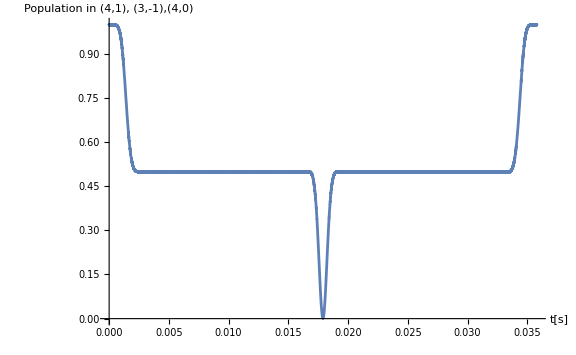

```mathematica
deqnb =Join[Flatten[eqnset,1],Flatten[init,1]];   (* Combine the differential equation and initial condition *)
sol1=NDSolve[deqnb/.{δrf->-Δ,δuw->Δ -(2Pi)*0.12*10^3}, {Subscript[c,4,2],Subscript[c,4,0],Subscript[c,4,1],Subscript[c,3,0],Subscript[c,3,-1],Subscript[c,3,-2]},{t,0,2*Te+3 *TPi}];
(* Solve the differential equation with numerical method *)
Plot[
Evaluate[(Abs[Subscript[c,3,-1][t]]^2)/.sol1],{t,0*10^-4,2*Te+3 *TPi},PlotRange->{-0.001,1.},PlotPoints->600,ImageSize->Large,AxesLabel->{Style["t[s]",FontSize->14],Style["Population in (4,1), (3,-1),(4,0)",FontSize->18]}]  (* Plot the result *)
```

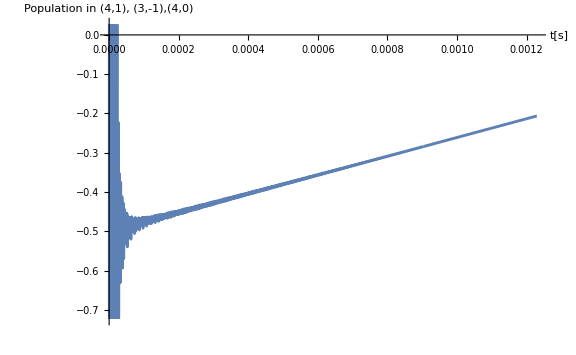

```mathematica
Plot[
Evaluate[(1/Pi*Arg[Subscript[c,4,1][t]/Subscript[c,3,-1][t]])/.sol1],{t,0*10^-4,Tpulse[π/2]},PlotRange->Automatic,PlotPoints->600,ImageSize->Large,AxesLabel->{Style["t[s]",FontSize->14],Style["Population in (4,1), (3,-1),(4,0)",FontSize->18]}]
```

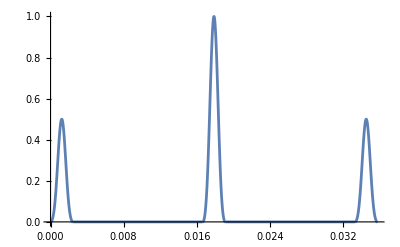

```mathematica
Plot[AmpRF[t],{t,0*10^-4,2*Te+3 *TPi},PlotRange->All]
```